# Метод на най-малките квадрати (МНМК)

Задача: (a и b са съответно предпоследната и последната цифра от факултетния номер)
1. Да се състави таблицата (x_k, g(x_k)), където
x_k =  -b + k(0.1), k = OverBar[0,10],   g(x) = ⅇ^(((a+1)x)/10)
Търси се апроксимацията в точката s = -b + (0.17)a + 0.01. За тази цел:
2. Да се построи полином на ленейна регресия по получената таблица.
3. Да се построи полином на квадратична регресия по получената таблица.
4. Да се построи полином на кубична регресия по получената таблица.
5. Да се пресметне апроксимацията, използвайки всеки един от построените полиноми (общо 3).
6. Да се оцени грешката за всяка от получените апроксимации.
7. Да се направи сравнение между трите резултата.

## Генериране на данни

```mathematica
a = 7.; b = 14;
n = 11;
h = (b - a)/n;
```

```mathematica
xt = Table[2+k*h, {k, 7, 14}]
```

{6.45455,7.09091,7.72727,8.36364,9.,9.63636,10.2727,10.9091}

```mathematica
f[x_] := (x +14) * Log[√(x + 13)]
yt = f[xt]
```

{30.3554,31.6392,32.9326,34.2353,35.547,36.8675,38.1966,39.534}

```mathematica
P = Length[xt]
```

8

### Визуализация

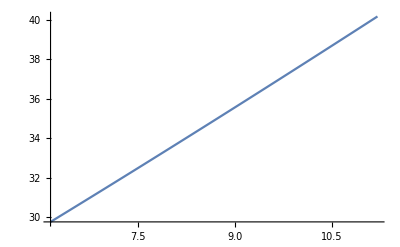

```mathematica
grf = Plot[f[x], {x, xt[[1]] - 0.3, xt[[P]] + 0.3}]
```

```mathematica
points = Table[{xt[[i]], yt[[i]]}, {i, 1, P}];
```

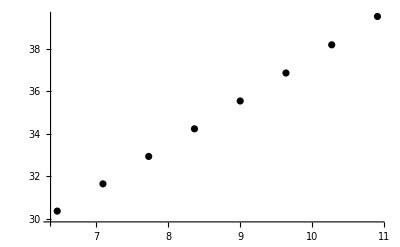

```mathematica
grp = ListPlot[points, PlotStyle->Black]
```

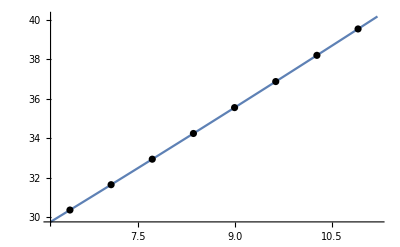

```mathematica
Show[grf, grp]
```

## Квадратична регресия

### Попълваме таблицата

```mathematica
xt^2
```

{41.6612,50.281,59.7107,69.9504,81.,92.8595,105.529,119.008}

```mathematica
yt*xt
```

{195.93,224.351,254.479,286.331,319.923,355.269,392.383,431.279}

```mathematica
xt^3
```

{268.904,356.538,461.401,585.04,729.,894.828,1084.07,1298.27}

```mathematica
xt^4
```

{1735.65,2528.18,3565.37,4893.06,6561.,8622.89,11136.4,14163.}

```mathematica
yt*xt^2
```

{1264.64,1590.85,1966.43,2394.77,2879.31,3423.5,4030.84,4704.87}

### Намиране на сумите

```mathematica
∑_(i=1)^P xt[[i]]
```

69.4545

```mathematica
∑_(i=1)^P yt[[i]]
```

279.307

```mathematica
∑_(i=1)^P xt[[i]]^2
```

620.

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]
```

2459.94

```mathematica
∑_(i=1)^P xt[[i]]^3
```

5678.05

```mathematica
∑_(i=1)^P xt[[i]]^4
```

53205.5

```mathematica
∑_(i=1)^P yt[[i]]*xt[[i]]^2
```

22255.2

### Решаваме системата

```mathematica
A = ({{P, ∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2}, {∑_(i=1)^P xt[[i]], ∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3}, {∑_(i=1)^P xt[[i]]^2, ∑_(i=1)^P xt[[i]]^3, ∑_(i=1)^P xt[[i]]^4}}); b={∑_(i=1)^P yt[[i]], ∑_(i=1)^P yt[[i]]*xt[[i]],  ∑_(i=1)^P yt[[i]]*xt[[i]]^2};
```

```mathematica
LinearSolve[A,b]
```

{17.8298,1.8694,0.0110169}

Таен коз (възможност за самопроверка)

```mathematica
Fit[points, {1, x, x^2}, x]
```

17.8298+1.8694 x+0.0110169 x^2

### Съставяме полинома

```mathematica
P2[x_] := 0.169855 - 0.0415066x + 0.0026155 x^2
```

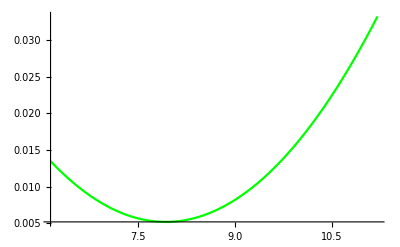

```mathematica
grfP2 = Plot[P2[x], {x, xt[[1]] - 0.3, xt[[P]] + 0.3}, PlotStyle->Green]
```

```mathematica
P2[-5.97]
```

0.510868

За сравнение истинската стойност

```mathematica
f[-5.97]
```

7.83

### Оценка на грешката

#### Теоретична грешка (средноквадратична)

```mathematica
√(∑_(i=1)^P (yt[[i]] - P2[xt[[i]]])^2)
```

99.0793

#### Истинска грешка

```mathematica
Abs[f[-5.97] - P2[-5.97]]
```

7.31913

## Леви правоъгълници

```mathematica
Plot[Abs[f'[x]],{x,a,b}]
```

Plot::plln: Limiting value {279.307,2459.94,22255.2} in {x,7.,{279.307,2459.94,22255.2}} is not a machine-sized real number.

Plot[Abs[f'[x]],{x,a,b}]

```mathematica
a = 7.;b= 14.;
h = (b -a)/n;
n = 11;
f[x_]:= (x +14) * Log[√(x + 13)]
Itochno = ∫_a^b f[x]ⅆx ;
I1 = h*∑_(i=0)^(n-1) f[a+i*h];
M1 = Abs[f'[a]];
R1 = (b-a)^2/(2n)*M1;
Print["Мрежата е със стъпка ", h, " и брой подинтервали ", n]
Print["Приближената стойност по формулата на левите правоъгълници е ", I1]
Print["Точната стойност                                           е ", Itochno]
Print["Теоретичната грешка по формулата на левите правоъгълници   е ", R1]
Print["Истинската грешка по формулата на левите правоъгълници     е ", Abs[I1-Itochno]]
```

Мрежата е със стъпка 0.636364 и брой подинтервали 11

Приближената стойност по формулата на левите правоъгълници е 266.336

Точната стойност                                           е 271.005

Теоретичната грешка по формулата на левите правоъгълници   е 4.50547

Истинската грешка по формулата на левите правоъгълници     е 4.66814